we have a pile of different associations / dictionaries. 
System is a pair (name,dimension). 
A (vector) space dictionary for a given single system records the system and its type (ket or bra). Call it AtomicSpace. 
General spaces associated with several systems are lists of AtomicSpaces. Call them Space.
Index dictionaries are lists of spaces, call them IndexDict.
Multilinear maps are given by a pair, an IndexDict and an Array, having the same dimensions. Call them MultiMap. (I.e. the IndexDict records which systems correspond to which indices in the Array.)

```mathematica
Unprotect[AtomicSpace,VecSpace,System,MapDict,IndexDict,MultiMap,Name,Dimension]
```

{AtomicSpace,VecSpace,System,MapDict,IndexDict,MultiMap,Name,Dimension}

#### MapDict

somewhat separately from this, we need to manipulate the mapping dictionary for multilinear maps: what are its inputs and what are its outputs. Can we compose two given maps in a given order? What systems will be contracted out when doing so? Etc. Call such a dictionary MapDict. It is two lists: a list of output system names and a list of input system names.

```mathematica
ContractableSystems[L_MapDict,R_MapDict]:=Intersection[L[[2]],R[[1]]];
```

```mathematica
ComposeMaps[L_MapDict,R_MapDict]:=
MapDict@@({Join[L[[1]],Complement[R[[1]],#]],Join[R[[2]],Complement[L[[2]],#]]}&[ContractableSystems[L,R]]);
NonCommutativeMultiply[MapDict[oL_,iL_],MapDict[oR_,iR_]]^:=ComposeMaps[MapDict[oL,iL],MapDict[oR,iR]]
```

```mathematica
ValidMappingQ[x_MapDict]:=And@@(DuplicateFreeQ/@x);
ComposableQ[L_MapDict,R_MapDict]:=ValidMappingQ[ComposeMaps[L,R]];
MappingEqualQ[x_MapDict,y_MapDict]:=Equal@@(Sort/@#&/@{x,y});
```

strictly speaking, partial traces are outside the scope of composition of multilinear maps. (one can do it by composing entangled states at input and output, but the point is it is not a composition itself)

```mathematica
ContractableSystems[x_MapDict]:=
ContractableSystems[x,x]; (* we don't seem to be using this yet; maybe for something like ContractAll *)
ContractableSystemQ[x_MapDict,sysname_]:=And@@(MemberQ[#,sysname]&/@x);
ContractableSystemsQ[x_MapDict,sysnames_List]:=And@@(SubsetQ[#,sysnames]&/@x);
```

```mathematica
ContractableSystems[MapDict[{"a"},{"b","a"}]]
```

{a}

```mathematica
ValidMappingQ[MapDict[{"a"},{"b","a"}]]
```

True

```mathematica
ContractableSystemsQ[MapDict[{"a"},{"b","a"}],{"a","b"}]
```

False

#### System

System is the ordered pair of the system name and its dimension. There’s no reason to have a constructor, just type “System” and give it these two things as arguments.

```mathematica
a=System["a",2];
b=System["b",4];
c=System["c",3];
d=System["d",7];
```

```mathematica
Name[x_System]:=x[[1]];
Dimension[x_System]:=x[[2]];
```

#### AtomicSpace

Atomic spaces are ordered triples of a system name, dimension, and one of the two strings “ket” or “bra”. The dimension information is present in

```mathematica
asp1=AtomicSpace[a,"ket"];
asp2=AtomicSpace[b,"bra"];
asp3=AtomicSpace[a,"bra"];
asp4=AtomicSpace[c,"ket"];
asp6=AtomicSpace[c,"bra"];
asp5=AtomicSpace[d,"ket"];
```

```mathematica
Name[x_AtomicSpace]:=Name[x[[1]]]
Dimension[x_AtomicSpace]:=Dimension[x[[1]]];
Type[x_AtomicSpace]:=x[[2]];
```

```mathematica
Type[asp1]
```

ket

```mathematica
Name[asp1]
```

a

#### VecSpace

General spaces are just lists of atomic spaces, but with head “VecSpace”

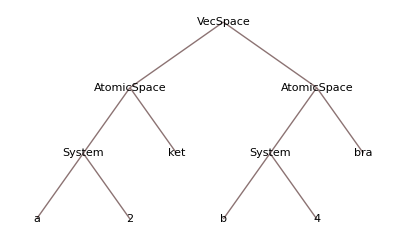

```mathematica
sp1=VecSpace[asp1,asp2];
sp2=VecSpace[asp3];
sp1//TreeForm
```

```mathematica
AtomNames[x_VecSpace]:=Level[x,{3}][[;;;;2]];
AtomicQ[x_VecSpace]:=Length[x]==1;
AtomDimensions[x_VecSpace]:=Level[x,{3}][[2;;;;2]];
Dimension[x_VecSpace]:=Times@@AtomDimensions[x];
```

```mathematica
AtomNames[sp1]
```

{a,b}

```mathematica
AtomNames[sp1]
```

{a,b}

to get the leaves, use Level {-1}

```mathematica
Map[List@@#&,sp1,{0,1}]
```

{{System[a,2],ket},{System[b,4],bra}}

```mathematica
Level[sp1,{-1}]
```

{a,2,ket,b,4,bra}

#### IndexDict

Index dictionary: list of vector spaces. Shouldn’t contain AtomicSpaces with the same name and type.

```mathematica
td1=IndexDict[sp1,sp2]
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
td2=IndexDict[VecSpace[AtomicSpace[b,"ket"]],VecSpace[AtomicSpace[d,"bra"]]]
```

IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]]]

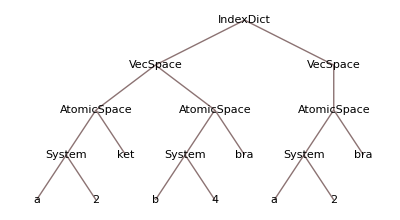

```mathematica
td1//TreeForm
```

```mathematica
Atoms[x_IndexDict]:=Level[x,{2}];
Atomize[x_IndexDict]:=IndexDict@@(VecSpace[#]&/@Atoms[x]);
AtomicQ[x_IndexDict]:=And@@(AtomicQ/@x);
AtomNames[x_IndexDict]:=Level[x,{4}][[;;;;2]]
```

```mathematica
(VecSpace[#]&/@Atoms[td1])
```

{VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]}

```mathematica
AtomicQ[Atomize[td1]]
```

True

```mathematica
(AtomicQ/@td1)
```

IndexDict[False,True]

```mathematica
Atomize[td1]
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
Kets[x_IndexDict]:=Select[Atoms[x],#[[2]]=="ket"&]
Bras[x_IndexDict]:=Select[Atoms[x],#[[2]]=="bra"&]
```

```mathematica
Bras[td1]
```

{AtomicSpace[System[b,4],bra],AtomicSpace[System[a,2],bra]}

```mathematica
Name/@Bras[td1]
```

{b,a}

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
SystemMapping[x_IndexDict]:=MapDict@@(Map[Name,{Kets[x],Bras[x]},{2}]);
ValidMappingQ[x_IndexDict]:=ValidMappingQ[SystemMapping[x]];
MappingEqualQ[x_IndexDict,y_IndexDict]:=MappingEqualQ[SystemMapping[x],SystemMapping[y]];
ComposableQ[L_IndexDict,R_IndexDict]:=ComposableQ[SystemMapping@L,SystemMapping@R]
```

```mathematica
ContractableSystemQ[x_IndexDict,sysname_]:=ContractableSystemQ[SystemMapping[x],sysname];
ContractableSystemsQ[x_IndexDict,sysnames_List]:=ContractableSystemsQ[SystemMapping[x],sysnames]
```

```mathematica
SystemMapping[td1]
```

MapDict[{a},{b,a}]

```mathematica
td2//SystemMapping
```

MapDict[{b},{d}]

these are for atomic IndexDicts only

```mathematica
NameSort[x_IndexDict/;AtomicQ[x]]:=IndexDict@@(VecSpace[#]&/@SortBy[Level[x,{2}],{Name,Type[#]=="bra"&}])
TypeSort[x_IndexDict/;AtomicQ[x]]:=IndexDict@@(VecSpace[#]&/@SortBy[Level[x,{2}],{Type[#]=="bra"&,Name}])
```

these as well. all of these are really bad in the sense that they would produce syntactically-valid output from non-atomic IndexDicts, but the outputs don’t mean anything useful in terms of the original object.

```mathematica
KetIndices[x_IndexDict]:=Flatten[Position[Atoms[x],z_/;Type[z]=="ket"]];
BraIndices[x_IndexDict]:=Flatten[Position[Atoms[x],z_/;Type[z]=="bra"]]
```

```mathematica
CompositionIndices[L_IndexDict,R_IndexDict]:=Flatten[{Position[Atoms@L,z_/;Type[z]=="bra"&&Name[z]==#],Position[Atoms@R,z_/;Type[z]=="ket"&&Name[z]==#]}]&/@(ContractableSystems@@(SystemMapping[#]&/@{L,R}));
```

```mathematica
ComposeMaps[L_IndexDict/;AtomicQ[L],R_IndexDict/;AtomicQ[R]]:=With[{ci=CompositionIndices[L,R]},
If[ci=={},IndexDict@@(Join[L,R]),IndexDict@@(Join@@MapThread[Delete,{{L,R},Transpose[{#}]&/@Transpose[ci]}])]]
```

```mathematica
ComposeMaps[Atomize[td1],td2]//SystemMapping
```

MapDict[{a},{a,d}]

```mathematica
ComposeMaps[td2,Atomize[td1]]//SystemMapping
```

MapDict[{b,a},{d,b,a}]

```mathematica
AtomicQ[td2]
```

True

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
ContractionIndices[x_IndexDict,sysnames_List]:=If[ContractableSystemsQ[x,sysnames],
With[{atoms=Atoms[x]},
Flatten[{Position[atoms,z_/;Type[z]=="bra"&&Name[z]==#],Position[atoms,z_/;Type[z]=="ket"&&Name[z]==#]}]&/@(sysnames)],{}]
```

```mathematica
ContractionIndices[td1,{"b"}]
```

{}

```mathematica
td2
```

IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]]]

```mathematica
ComposeMaps[td2,Atomize[td1]]//SystemMapping
```

MapDict[{b,a},{d,b,a}]

```mathematica
?ContractableSystemsQ
```

Global`ContractableSystemsQ

ContractableSystemsQ[x_MapDict,sysnames_List]:=And@@(SubsetQ[#1,sysnames]&)/@x
 
ContractableSystemsQ[x_IndexDict,sysnames_List]:=ContractableSystemsQ[SystemMapping[x],sysnames]

```mathematica
ContractMap2[x_IndexDict/;AtomicQ[x],sysnames_List]:=With[{ci=ContractionIndices[x,sysnames]},
If[ci=={},,Delete[x,Transpose[ci]]]]
```

```mathematica
ContractMap[x_IndexDict,sysnames_List]:=If[ContractableSystemsQ[x,sysnames],Module[{r=Select[Atoms[x],!MemberQ[sysnames,Name[#]]&]},If[r=={},IndexDict[],IndexDict[VecSpace@@r]]]]
```

```mathematica
ContractMap2[td1,{"a"}]
```

IndexDict[VecSpace[AtomicSpace[System[b,4],bra]]]

```mathematica
Select[Atoms[td1],Name[#]=="a"&]
```

{AtomicSpace[System[a,2],ket],AtomicSpace[System[a,2],bra]}

```mathematica
Atoms[td1]
```

{a,b,a}

```mathematica
td3//SystemMapping
```

MapDict[{a,b},{b,a}]

```mathematica
Clear[ContractMap]
```

```mathematica
Atoms[Atomize[td3]]
```

{AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra],AtomicSpace[System[a,2],bra],AtomicSpace[System[b,4],ket]}

```mathematica
ContractMap[Atomize[td3],{"a","b"}]
```

IndexDict[]

```mathematica
ContractionIndices[Atomize[td3],{"a","b"}]
```

{{3,1},{2,4}}

#### MultiMap

it seems that we have to separately deal with the exceptional case of maps from C to C (i.e. numbers). This case is exceptional because the array in the second slot of MultiMap is now just a number; it has no dimensions, and so it doesn’t work with ArrayReshape.

```mathematica
AtomicQ[t_MultiMap]:=And[AtomicQ[t[[1]]],List@@Dimension/@Atoms[t[[1]]]==Dimensions[t[[2]]]];Atomize[t_MultiMap]:=
If[AtomicQ[t],t,
Module[{atomdict=Atomize[t[[1]]]},
MultiMap@@{atomdict,ArrayReshape[t[[2]],List@@Dimension/@atomdict]}]];
```

```mathematica
MappingEqualQ[t1_MultiMap,t2_MultiMap]:=MappingEqualQ[t1[[1]],t2[[1]]];
```

```mathematica
ComposableQ[L_MultiMap,R_MultiMap]:=ComposableQ[L[[1]],R[[1]]];
```

```mathematica
ComposeAtomicTensors[L_MultiMap,R_MultiMap]:=If[ComposableQ[L[[1]],R[[1]]],MultiMap@@{ComposeMaps[L[[1]],R[[1]]],Activate[TensorContract[Inactive[TensorProduct][L[[2]],R[[2]]],(#+{0,Length[L[[1]]]})&/@CompositionIndices[L[[1]],R[[1]]]]]}]
```

```mathematica
ComposeMaps[L_MultiMap,R_MultiMap]:=ComposeAtomicTensors[Atomize[L],Atomize[R]];
```

```mathematica
Times[MultiMap[x_,y_],z_?NumericQ]^:=MultiMap[x,z y];
NonCommutativeMultiply[MultiMap[x1_,x2_],MultiMap[y1_,y2_]]^:=ComposeMaps[MultiMap[x1,x2],MultiMap[y1,y2]];
```

```mathematica
ComposeMaps[x_MultiMap]:=x;
```

```mathematica
ComposeMaps[L_MultiMap,R_MultiMap]:=ComposeAtomicTensors[Atomize[L],Atomize[R]];
```

```mathematica
ComposeMaps[L_MultiMap,R_MultiMap,x__MultiMap]:=ComposeMaps[ComposeMaps[L,R],ComposeMaps[x]]
```

```mathematica
SystemMapping[t_MultiMap]:=SystemMapping[t[[1]]]
```

```mathematica
t1=MultiMap[td1,RandomReal[{0,1},{8,2}]];
t2=MultiMap[td2,RandomReal[{0,1},{4,7}]];
testket=MultiMap[IndexDict[VecSpace[AtomicSpace[System["a",2],"ket"]]],RandomReal[{0,1},{2}]];
testbra=MultiMap[IndexDict[VecSpace[AtomicSpace[System["a",2],"bra"]]],RandomReal[{0,1},{2}]];
trivial=ComposeAtomicTensors[testbra,testket];
```

```mathematica
SystemMapping[t1]
```

MapDict[{a},{b,a}]

```mathematica
t1
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]],{{0.034183,0.00747514},{0.412888,0.0112735},{0.320335,0.588377},{0.293249,0.901237},{0.644652,0.132433},{0.194547,0.710976},{0.0311794,0.0801829},{0.643045,0.885508}}]

```mathematica
t1 **t2
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[d,7],bra]]],{{{0.365392,0.305588,0.636108,0.528864,0.511837,0.711716,0.63758},{0.335002,0.477467,0.645376,0.8256,0.760312,0.936721,0.633086}},{{0.678357,0.540051,1.13432,0.667508,1.03265,1.2602,0.857353},{0.583009,0.730332,1.33885,0.599249,0.960397,1.61861,1.22169}}}]

```mathematica
ComposeMaps[t1,t2]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[d,7],bra]]],{{{0.365392,0.305588,0.636108,0.528864,0.511837,0.711716,0.63758},{0.335002,0.477467,0.645376,0.8256,0.760312,0.936721,0.633086}},{{0.678357,0.540051,1.13432,0.667508,1.03265,1.2602,0.857353},{0.583009,0.730332,1.33885,0.599249,0.960397,1.61861,1.22169}}}]

```mathematica
t1//SystemMapping
```

MapDict[{a},{b,a}]

```mathematica
t
```

```mathematica
10t1
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]],{{0.34183,0.0747514},{4.12888,0.112735},{3.20335,5.88377},{2.93249,9.01237},{6.44652,1.32433},{1.94547,7.10976},{0.311794,0.801829},{6.43045,8.85508}}]

```mathematica
ComposeMaps[t1,t2]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[d,7],bra]]],{{{0.365392,0.305588,0.636108,0.528864,0.511837,0.711716,0.63758},{0.335002,0.477467,0.645376,0.8256,0.760312,0.936721,0.633086}},{{0.678357,0.540051,1.13432,0.667508,1.03265,1.2602,0.857353},{0.583009,0.730332,1.33885,0.599249,0.960397,1.61861,1.22169}}}]

```mathematica
ComposeMaps[t2,t1,testket]//SystemMapping
```

MapDict[{b,a},{d,b}]

```mathematica
ComposeMaps[testbra,t2,t1,testket]//SystemMapping
```

MapDict[{b},{d,b}]

```mathematica
ComposeMaps[testbra,t2,t1,testket]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]],VecSpace[AtomicSpace[System[b,4],bra]]],{{{0.118251,0.0996769,0.0547553,0.1825},{0.034667,0.0292217,0.0160523,0.0535023},{0.133696,0.112695,0.0619068,0.206336},{0.0997426,0.0840756,0.0461851,0.153935},{0.140135,0.118123,0.0648884,0.216274},{0.109465,0.0922712,0.0506872,0.168941},{0.0797917,0.0672584,0.036947,0.123144}},{{0.0728003,0.0613652,0.0337096,0.112354},{0.0541571,0.0456504,0.025077,0.0835819},{0.147286,0.124151,0.0681995,0.227309},{0.0437724,0.0368969,0.0202685,0.067555},{0.0697779,0.0588175,0.0323101,0.10769},{0.144367,0.12169,0.066848,0.222805},{0.147363,0.124216,0.0682352,0.227428}},{{0.0520037,0.0438352,0.0240799,0.0802585},{0.00248473,0.00209444,0.00115053,0.00383474},{0.0184293,0.0155345,0.00853356,0.0284424},{0.153405,0.129309,0.0710329,0.236753},{0.066021,0.0556508,0.0305705,0.101892},{0.0102903,0.00867395,0.00476485,0.0158813},{0.0381276,0.0321387,0.0176547,0.0588432}},{{0.0225104,0.0189745,0.0104233,0.0347408},{0.0805809,0.0679237,0.0373124,0.124362},{0.0974325,0.0821283,0.0451154,0.15037},{0.0422821,0.0356406,0.0195784,0.0652549},{0.0872983,0.073586,0.0404229,0.13473},{0.153732,0.129584,0.0711843,0.237258},{0.0828778,0.0698598,0.0383759,0.127907}}}]

```mathematica
Atomize[testbra]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],bra]]],{0.450867,0.102993}]

```mathematica
genPerm[list1_,list2_]:=Flatten[Position[list1,#]&/@list2];
SortMap[x_IndexDict/;AtomicQ[x],f_]:=genPerm[List@@(f[x]),List@@x]
```

```mathematica
SortMap[Atomize[td1],TypeSort]
```

{1,3,2}

Canonical is kets then bras, i.e. Type sorted.

```mathematica
Canonicalize[t_MultiMap]:=
If[Length[t[[1]]]==0,t,MultiMap@@{TypeSort[#[[1]]],Transpose[#[[2]],SortMap[#[[1]],TypeSort]]}&[Atomize[t]]];
AddMaps[t1_MultiMap,t2_MultiMap]:=If[MappingEqualQ[t1,t2],Module[{ct1=Canonicalize[t1]},MultiMap[ct1[[1]],ct1[[2]]+Canonicalize[t2][[2]]]]];
Plus[MultiMap[x1_,y1_],MultiMap[x2_,y2_]]^:=AddMaps[MultiMap[x1,y1],MultiMap[x2,y2]]
```

```mathematica
Matrixize[t_MultiMap]:=
Module[{ct,keti,brai},
ct=Canonicalize[t];
keti=KetIndices[ct[[1]]];
brai=BraIndices[ct[[1]]];
Which[
keti=={}&&brai=={},
MultiMap[IndexDict[],ct[[2]]],
keti=={}||brai=={},
MultiMap[IndexDict[VecSpace@@Atoms[ct[[1]]]],Flatten[ct[[2]]]],
True,
MultiMap@@({IndexDict@@(VecSpace@@#&/@SplitBy[Atoms[ct[[1]]],Type]),Flatten[ct[[2]],{keti,brai}]})]]
```

```mathematica
t1
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]],{{0.034183,0.00747514},{0.412888,0.0112735},{0.320335,0.588377},{0.293249,0.901237},{0.644652,0.132433},{0.194547,0.710976},{0.0311794,0.0801829},{0.643045,0.885508}}]

```mathematica
t1//Head
```

MultiMap

```mathematica
SplitBy[Atoms[t1[[1]]],Type]
```

{{AtomicSpace[System[a,2],ket]},{AtomicSpace[System[b,4],bra],AtomicSpace[System[a,2],bra]}}

```mathematica
Canonicalize[trivial]
```

MultiMap[IndexDict[],0.411267]

```mathematica
ComposeMaps[t2,t1]//SystemMapping
```

MapDict[{b,a},{d,b,a}]

```mathematica
Matrixize[ComposeMaps[t2,t1]][[2]]//SingularValueList
```

{5.69956,2.05113,1.84173,1.082,0.662792,0.596866,0.389383,0.214797}

```mathematica
td1//TreeForm
```

-Graphics-

```mathematica
Type[AtomicSpace[System["testname",32],"ket"]]
```

ket

#### PartialTranspose

supports lists of system names.7f, as in qmatrix.

partial transpose swaps ket and bra for a given system in the index list. actually it renames one to the other.

```mathematica
KetAddress[x_IndexDict,sysname_]:=Position[x,z_/;Name[z]==sysname&&Type[z]=="ket",{2}];
BraAddress[x_IndexDict,sysname_]:=Position[x,z_/;Name[z]==sysname&&Type[z]=="bra",{2}]
```

```mathematica
KetAddresses[x_IndexDict,sysnames_List]:=Position[x,z_/;MemberQ[sysnames,Name[z]]&&Type[z]=="ket",{2}];
BraAddresses[x_IndexDict,sysnames_List]:=Position[x,z_/;MemberQ[sysnames,Name[z]]&&Type[z]=="bra",{2}]
```

```mathematica
PartialTranspose[x_IndexDict,sysnames_List]:=If[ContractableSystemsQ[x,sysnames],Module[{k=Join[#,{2}]&/@KetAddresses[x,sysnames],b=Join[#,{2}]&/@BraAddresses[x,sysnames]},
ReplacePart[x,{k->"bra",b->"ket"}]]]
```

```mathematica
PartialTranspose[x_MultiMap,sysnames_List]:=MultiMap[PartialTranspose[x[[1]],sysnames],x[[2]]]
```

```mathematica
td3=IndexDict[VecSpace[AtomicSpace[System["a",2],"ket"],AtomicSpace[System["b",4],"bra"]],VecSpace[AtomicSpace[System["a",2],"bra"]],VecSpace[AtomicSpace[System["b",4],"ket"]]];
```

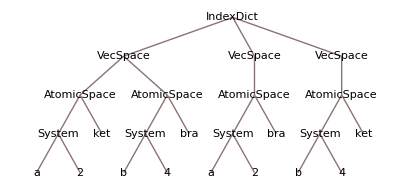

```mathematica
td3//TreeForm
```

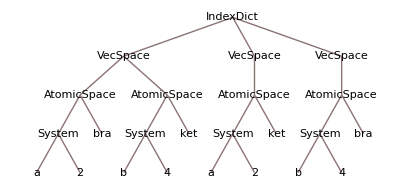

```mathematica
PartialTranspose[td3,{"a","b"}]//TreeForm
```

#### Adjoint, Transpose

Transpose, just interchanging kets to bras, is a hack for the actual transpose of the map; if the map goes from U to V, then the transpose goes from V* to U*. Interchanging kets / bras gives a map from V to U again, which has the same action as the actual transpose, once we identify a basis in U with one in U* and same for V.

```mathematica
KetAddresses[x_IndexDict]:=Position[x,z_/;Type[z]=="ket",{2}];
BraAddresses[x_IndexDict]:=Position[x,z_/;Type[z]=="bra",{2}]
```

```mathematica
MapTranspose[x_MultiMap]:=MultiMap[Module[{k=Join[#,{2}]&/@KetAddresses[x[[1]]],b=Join[#,{2}]&/@BraAddresses[x[[1]]]},
ReplacePart[x[[1]],{k->"bra",b->"ket"}]],x[[2]]]
```

```mathematica
Transpose[MultiMap[x_,y_]]^:=MapTranspose[MultiMap[x,y]]
```

```mathematica
Adjoint[x_MultiMap]:=MultiMap[Module[{k=Join[#,{2}]&/@KetAddresses[x[[1]]],b=Join[#,{2}]&/@BraAddresses[x[[1]]]},
ReplacePart[x[[1]],{k->"bra",b->"ket"}]],Conjugate[x[[2]]]]
```

```mathematica
t1
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]],{{0.034183,0.00747514},{0.412888,0.0112735},{0.320335,0.588377},{0.293249,0.901237},{0.644652,0.132433},{0.194547,0.710976},{0.0311794,0.0801829},{0.643045,0.885508}}]

```mathematica
Transpose[t1]==Adjoint[t1]
```

True

```mathematica
KetAddresses[td3]
```

{{1,1},{3,1}}

#### PartialTrace

need to port the composition stuff to contraction here.

```mathematica
PartialTrace[x_MultiMap/;AtomicQ[x],sysnames_List]:=
If[ContractableSystemsQ[x[[1]],sysnames],MultiMap[ContractMap[x[[1]],sysnames],TensorContract[x[[2]],ContractionIndices[x[[1]],sysnames]]]]
```

#### Constructors

```mathematica
basisElement[sys_,num_,type_]:=MultiMap@@{IndexDict[VecSpace[AtomicSpace[sys,type]]],SparseArray[{num+1->1},{Dimension[sys]}]};basisKet[sys_,num_]:=
basisElement[sys,num,"ket"];
basisBra[sys_,num_]:=basisElement[sys,num,"bra"];
```

we can use some transpose trickery to generate the entangled state easily. it’s just the KroneckerDelta representation of the identity matrix on a compound state space mapped over to omega by reordering the tensor factors. (obviously)

```mathematica
OmegaKet[sys1_System,sys2_System]:=MultiMap[IndexDict[VectorSpace[AtomicSpace[sys1,"ket"]],VectorSpace[AtomicSpace[sys2,"ket"]]],SparseArray@Flatten[IdentityMatrix[Dimension@sys1]]];
OmegaBra[sys1_System,sys2_System]:=MultiMap[IndexDict[VectorSpace[AtomicSpace[sys1,"bra"]],VectorSpace[AtomicSpace[sys2,"bra"]]],SparseArray@Flatten[IdentityMatrix[Dimension@sys1]]];
OmegaOp[sys1_,sys2_]:=MultiMap[IndexDict[VectorSpace[AtomicSpace[sys1,"ket"],AtomicSpace[sys1,"bra"]],VectorSpace[AtomicSpace[sys2,"ket"],AtomicSpace[sys2,"bra"]]],SparseArray[IdentityMatrix[(Dimension@sys1)^2]]]
```

```mathematica
Swap[sys1_System,sys2_System]:=PartialTranspose
```

```mathematica
?Swap
```

Information::notfound: Symbol "Swap" not found.

```mathematica
Dimension[c]
```

2

constructing MultiMaps from matrix representatives. The matrices act to the right...

```mathematica
fromMatrix[systems_List,matrix_]:=MultiMap[IndexDict[VecSpace@@(AtomicSpace[#,"ket"]&/@systems),VecSpace@@(AtomicSpace[#,"bra"]&/@systems)],SparseArray@matrix]
```

```mathematica
fromMatrix[sysout_List,sysin_List,matrix_]:=MultiMap[IndexDict[VecSpace@@(AtomicSpace[#,"ket"]&/@sysout),VecSpace@@(AtomicSpace[#,"bra"]&/@sysin)],SparseArray@matrix]
```

```mathematica
Matrixize[makeOmegaOp[a,b[1]]]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b[1],2],ket]],VecSpace[AtomicSpace[System[a,2],bra],AtomicSpace[System[b[1],2],bra]]],{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}}]

```mathematica
makeOmegaOp[sys1_,sys2_]:={{{makeSpace[sys1,"ket"],makeSpace[sys1,"bra"]},{makeSpace[sys2,"ket"],makeSpace[sys2,"bra"]}},IdentityMatrix[sys1["dim"]^2]}
```

```mathematica
basisElement[a,1,"ket"]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]]],SparseArray[<1>, {2}]]

```mathematica
testket
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]]],{0.549284,0.259767}]

```mathematica
ComposeMaps[basisBra[a,0],testket]
```

MultiMap[IndexDict[],0.549284]

```mathematica
SystemMapping[t2]
SystemMapping[t1]
```

MapDict[{b},{d}]

MapDict[{a},{b,a}]

```mathematica
Canonicalize[t1]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[b,4],bra]]],{{{0.398351,0.330669,0.874514,0.789326},{0.969347,0.99864,0.00259545,0.998205}},{{0.432152,0.467101,0.924672,0.72963},{0.239969,0.420696,0.305539,0.477364}}}]

```mathematica
KetIndices[MultiMap[IndexDict[],0.29597124389250995]]
```

KetIndices[MultiMap[IndexDict[],0.295971]]

```mathematica
testket[[2]]//Norm
```

0.607611

```mathematica
{testket[[2]]}//SingularValueList
```

{0.607611}

```mathematica
makeCanonical[t1]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

Transpose::list: List expected at position 2 in Transpose[MultiMap[IndexDict[VecSpace[AtomicSpace[System["a", 2], "ket"]], VecSpace[AtomicSpace[System["b", 4], "bra"]], VecSpace[AtomicSpace[System["a", 2], "bra"]]], {{0.15965, 0.348782}, {0.0971431, 0.109028}, « 5 », {0.652819, 0.269328}}], Flatten[False]].

MultiMap[TypeSort[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]==IndexDict[]],Transpose[MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]],{{0.15965,0.348782},{0.0971431,0.109028},{0.102568,0.648692},{0.802404,0.187038},{0.395949,0.84404},{0.177322,0.528443},{0.431452,0.622575},{0.652819,0.269328}}],Flatten[False]]]

```mathematica
VecSpace@@Atoms[td1]
```

VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra],AtomicSpace[System[a,2],bra]]

```mathematica
List@@Dimension/@IndexDict[]
```

{}

```mathematica
testket
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]]],{0.180653,0.905646}]

```mathematica
Atomize[IndexDict[]]
```

IndexDict[]

```mathematica
makeCanonical[MultiMap[IndexDict[],0.3479437041322474]]
```

Transpose::list: List expected at position 2 in Transpose[0.347944, IndexDict[]].

MultiMap[IndexDict[],Transpose[0.347944,IndexDict[]]]

```mathematica
TypeSort[IndexDict[]]
```

IndexDict[]

```mathematica
SystemMapping[MultiMap[IndexDict[],0.3479437041322474]]
```

MapDict[{},{}]

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
Dimension[VecSpace[]]
```

Part::take: Cannot take positions 2 through -1 in {}.

{}

```mathematica
AtomicQ[t1]
```

False

```mathematica
AtomicQ[Atomize[t1]]
```

True

```mathematica
Dimension/@Atoms[td1]
```

{2,4,2}

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

MultiMap[IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]]],{{0.53438,0.287995,0.64531,0.53736,0.481176,0.39282,0.541349},{0.0494161,0.0824318,0.887234,0.164378,0.473109,0.277107,0.674586},{0.134865,0.528914,0.984423,0.187782,0.13805,0.801253,0.595785},{0.705281,0.138256,0.354786,0.439544,0.989133,0.685008,0.813878}}]

```mathematica
AtomicQ[td2]
```

True

```mathematica
AtomicQ[t2]
```

True

```mathematica
ComposeAtomicTensors[Atomize[t1],t2]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[d,7],bra]]],{{{0.669867,0.219173,0.574864,0.47371,0.930623,0.721469,0.866125},{0.41117,0.478397,1.02675,0.409367,0.493965,0.81511,0.801069}},{{0.738959,0.447106,1.06918,0.609877,0.979701,0.997563,1.12233},{0.751067,0.653165,1.72195,0.775708,1.00849,1.16132,1.40352}}}]

```mathematica
Dimension/@ComposeAtomicTensors[t2,Atomize[t1]][[1]]
```

IndexDict[4,7,2,4,2]

```mathematica
Dimensions[ComposeAtomicTensors[t2,Atomize[t1]][[2]]]
```

{4,7,2,4,2}

```mathematica
makeAtomic[t1][[1]]//AtomicQ
```

True

```mathematica
ComposeAtomicTensors[t2,Atomize[t1]][[1]]
```

IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]],VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
List@@Dimension/@Atomize[td1]
```

{2,4,2}